```mathematica
Ei=(Ep Eq - pxp pxq)/mir;
pz=pzp;
Ep=Epp;
pxp=cosy pxpp + siny pzpp;
pzp=cosy pzpp - siny pxpp;
Epp=(mir+(mi^2-mr^2)/mir)/2;
pzpp=Epp-(mi^2-t)/(2Eap);
ptpp=Sqrt[Epp^2-mi^2-pzpp^2];
pxpp=ptpp cosphi;
```

```mathematica
Ei
pz
```

1/2 Eq (mir+(mi^2-mr^2)/mir)-pxq (cosphi cosy √(-mi^2+1/4 (mir+(mi^2-mr^2)/mir)^2-(1/2 (mir+(mi^2-mr^2)/mir)-(mi^2-t)/(2 Eap))^2)+siny (1/2 (mir+(mi^2-mr^2)/mir)-(mi^2-t)/(2 Eap)))

-cosphi siny √(-mi^2+1/4 (mir+(mi^2-mr^2)/mir)^2-(1/2 (mir+(mi^2-mr^2)/mir)-(mi^2-t)/(2 Eap))^2)+cosy (1/2 (mir+(mi^2-mr^2)/mir)-(mi^2-t)/(2 Eap))

```mathematica
Solve[Ei==Sqrt[ETimin^2+pz^2],t]
```

$Aborted

```mathematica
Solve[(Ei^2-pz^2)==ETimin^2/.{mi->0 ,mr->0},t]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{t→-((Eap mir (cosy^4+2 cosphi^2 cosy^4 pxq^2+cosphi^4 cosy^4 pxq^4+16+cosphi^4 siny^4+2 cosphi^2 pxq^2 siny^4+pxq^4 siny^4))/(cosy^4+2 cosphi^2 cosy^4 pxq^2+cosphi^4 cosy^4 pxq^4+2 cosphi^2 cosy^2 siny^2-2 cosy^2 pxq^2 siny^2+8 3 siny^2-2 cosphi^4 cosy^2 pxq^2 siny^2+2 cosphi^2 cosy^2 pxq^4 siny^2+cosphi^4 siny^4+2 cosphi^2 pxq^2 siny^4+pxq^4 siny^4))-1/2 1-1/2 √1},2,{t→-(Eap mir (1))/(cosy^4+11+1)+1+1/2 1}}
 |  |  |  |

```mathematica
%//FullSimplify
```

((cosy (Eap mir+t)-cosphi Eap siny √(-(t (2 Eap mir+t))/Eap^2))^2+(Eap Eq mir-pxq (Eap mir siny+siny t+cosphi cosy Eap √(-(t (2 Eap mir+t))/Eap^2)))^2)/(4 Eap^2)

```mathematica
%//Expand
```

(cosy^2 mir^2)/4+(Eq^2 mir^2)/4-1/2 Eq mir^2 pxq siny+1/4 mir^2 pxq^2 siny^2+(cosy^2 mir t)/(2 Eap)-(cosphi^2 cosy^2 mir pxq^2 t)/(2 Eap)-(Eq mir pxq siny t)/(2 Eap)-(cosphi^2 mir siny^2 t)/(2 Eap)+(mir pxq^2 siny^2 t)/(2 Eap)+(cosy^2 t^2)/(4 Eap^2)-(cosphi^2 cosy^2 pxq^2 t^2)/(4 Eap^2)-(cosphi^2 siny^2 t^2)/(4 Eap^2)+(pxq^2 siny^2 t^2)/(4 Eap^2)-1/2 cosphi cosy Eq mir pxq √(-(t (2 Eap mir+t))/Eap^2)-1/2 cosphi cosy mir siny √(-(t (2 Eap mir+t))/Eap^2)+1/2 cosphi cosy mir pxq^2 siny √(-(t (2 Eap mir+t))/Eap^2)-(cosphi cosy siny t √(-(t (2 Eap mir+t))/Eap^2))/(2 Eap)+(cosphi cosy pxq^2 siny t √(-(t (2 Eap mir+t))/Eap^2))/(2 Eap)

```mathematica
%//FullSimplify
```

1/(4 Eap^2)(Eap^2 mir^2 (Eq-pxq siny)^2-2 Eap mir siny (Eq pxq+(cosphi-pxq) (cosphi+pxq) siny) t+(-cosphi^2+pxq^2) siny^2 t^2-2 cosphi cosy Eap √(-(t (2 Eap mir+t))/Eap^2) (Eap mir (siny+pxq (Eq-pxq siny))-(-1+pxq^2) siny t)+cosy^2 (Eap^2 mir^2-2 Eap mir (-1+cosphi^2 pxq^2) t+(1-cosphi^2 pxq^2) t^2))

```mathematica
D[(Ei^2+pz^2),t]
```

-2 pxq (1/2 Eq (mir+(mi^2-mr^2)/mir)-pxq (cosphi cosy √(-mi^2+1/4 (mir+(mi^2-mr^2)/mir)^2-(1/2 (mir+(mi^2-mr^2)/mir)-(mi^2-t)/(2 Eap))^2)+siny (1/2 (mir+(mi^2-mr^2)/mir)-(mi^2-t)/(2 Eap)))) (siny/(2 Eap)-(cosphi cosy (1/2 (mir+(mi^2-mr^2)/mir)-(mi^2-t)/(2 Eap)))/(2 Eap √(-mi^2+1/4 (mir+(mi^2-mr^2)/mir)^2-(1/2 (mir+(mi^2-mr^2)/mir)-(mi^2-t)/(2 Eap))^2)))+2 (-cosphi siny √(-mi^2+1/4 (mir+(mi^2-mr^2)/mir)^2-(1/2 (mir+(mi^2-mr^2)/mir)-(mi^2-t)/(2 Eap))^2)+cosy (1/2 (mir+(mi^2-mr^2)/mir)-(mi^2-t)/(2 Eap))) (cosy/(2 Eap)+(cosphi siny (1/2 (mir+(mi^2-mr^2)/mir)-(mi^2-t)/(2 Eap)))/(2 Eap √(-mi^2+1/4 (mir+(mi^2-mr^2)/mir)^2-(1/2 (mir+(mi^2-mr^2)/mir)-(mi^2-t)/(2 Eap))^2)))

```mathematica
%//FullSimplify
```

$Aborted

```mathematica
Solve[(Ei^2-pz^2)==ETimin^2/.{mi->0,mr->0,pxq->0,Eq->2 Eap,siny->0 ,cosy->1},t]//FullSimplify
```

{{t→-Eap (2 √((Eap-ETimin) (Eap+ETimin))+mir)},{t→Eap (2 √((Eap-ETimin) (Eap+ETimin))-mir)}}

```mathematica
Solve[(mir-Ei)^2-pz^2==ETrmin^2/.{mi->0,mr->0,pxq->0,Eq->2 Eap,siny->0 ,cosy->1},t]//FullSimplify
```

{{t→-Eap (2 √((Eap-ETrmin-mir) (Eap+ETrmin-mir))+mir)},{t→Eap (2 √((Eap-ETrmin-mir) (Eap+ETrmin-mir))-mir)}}

```mathematica
Solve[(Ei^2-pz^2)==ETimin^2/.{mi->0,mr->0,pxq->0,Eq->2 Eap},t]//FullSimplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

```mathematica
(Ei^2-pz^2)==ETimin^2/.{mi->0,mr->0,pxq->0,Eq->2 Eap}
```

Eap^2-(cosy (mir/2+t/(2 Eap))-cosphi siny √(mir^2/4-(mir/2+t/(2 Eap))^2))^2==ETimin^2

```mathematica
(Ei^2-pz^2)==ETimin^2
```

((1/2 Eq (mir+(mi^2-mr^2)/mir)-pxq (cosphi cosy √(-mi^2+1/4 (mir+(mi^2-mr^2)/mir)^2-(1/2 (mir+(mi^2-mr^2)/mir)-(mi^2-t)/(2 Eap))^2)+siny (1/2 (mir+(mi^2-mr^2)/mir)-(mi^2-t)/(2 Eap))))^2)/mir^2-(-cosphi siny √(-mi^2+1/4 (mir+(mi^2-mr^2)/mir)^2-(1/2 (mir+(mi^2-mr^2)/mir)-(mi^2-t)/(2 Eap))^2)+cosy (1/2 (mir+(mi^2-mr^2)/mir)-(mi^2-t)/(2 Eap)))^2==ETimin^2

```mathematica
Remove["Global`*"]
```

```mathematica
Ei=(Ep Eq - pxp pxq)/mir;
pz=pzp;
Ep=Epp;
pxp=cosy pxpp + siny pzpp;
pzp=cosy pzpp - siny pxpp;
ptpp=Sqrt[Epp^2-mi^2-pzpp^2];
pxpp=ptpp cosphi;
```

```mathematica
Ei^2-pz^2==ETimin^2
```

-(cosy pzpp-cosphi √(Epp^2-mi^2-pzpp^2) siny)^2+((Epp Eq-pxq (cosphi cosy √(Epp^2-mi^2-pzpp^2)+pzpp siny))^2)/mir^2==ETimin^2

```mathematica
Solve[Ei^2-pz^2==ETimin^2,pzpp]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{pzpp→(Epp Eq pxq siny (-cosy^2 mir^2+2 cosphi^2 cosy^2 mir^2+cosphi^2 cosy^2 pxq^2+cosphi^2 mir^2 siny^2+pxq^2 siny^2))/(cosy^4 mir^4+2 cosphi^2 cosy^4 mir^2 pxq^2+cosphi^4 cosy^4 pxq^4+2 cosphi^2 cosy^2 mir^4 siny^2-2 3 siny^2+1-1+2 cosphi^2 cosy^2 pxq^4 siny^2+cosphi^4 mir^4 siny^4+2 cosphi^2 mir^2 pxq^2 siny^4+pxq^4 siny^4)-1/2 √(1/1^2+2+1)-1/2 √((8 4 (1)^2)/(1)^2+7)},2,{pzpp→1}}
 |  |  |  |

```mathematica
Solve[D[Ei^2-pz^2,pzpp]==0,pzpp]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{pzpp→(Epp Eq pxq siny (-cosy^2 mir^2+2 cosphi^2 cosy^2 mir^2+cosphi^2 cosy^2 pxq^2+cosphi^2 mir^2 siny^2+pxq^2 siny^2))/(2 (cosy^4 mir^4+2 cosphi^2 cosy^4 mir^2 pxq^2+cosphi^4 cosy^4 pxq^4+6+2 cosphi^2 cosy^2 pxq^4 siny^2+cosphi^4 mir^4 siny^4+2 cosphi^2 mir^2 pxq^2 siny^4+pxq^4 siny^4))-1/2 √1-1/2 √((2 Epp^2 Eq^2 pxq^2 siny^2 (1)^2)/(1)^2-(4 (1))/(3 (1))-1/1-1/1-1/(4 √1))},2,{pzpp→1}}
 |  |  |  |

```mathematica
D[Ei^2-pz^2,pzpp]//FullSimplify
```

1/mir^2 2 (-cosy^2 (mir^2+cosphi^2 pxq^2) pzpp+siny (-Epp Eq pxq+(cosphi^2 mir^2+pxq^2) pzpp siny)+(cosphi cosy (Epp Eq pxq pzpp+(mir^2+pxq^2) (Epp^2-mi^2-2 pzpp^2) siny))/(√(Epp^2-mi^2-pzpp^2)))

```mathematica
Ei//FullSimplify
```

(Epp Eq-pxq (cosphi cosy √(Epp^2-mi^2-pzpp^2)+pzpp siny))/mir

```mathematica
Solve[(Ei^2-pz^2)==ETimin^2,pzpp]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{pzpp→(Epp Eq pxq siny (-cosy^2 mir^2+2 cosphi^2 cosy^2 mir^2+cosphi^2 cosy^2 pxq^2+cosphi^2 mir^2 siny^2+pxq^2 siny^2))/(cosy^4 mir^4+2 cosphi^2 cosy^4 mir^2 pxq^2+cosphi^4 cosy^4 pxq^4+2 cosphi^2 cosy^2 mir^4 siny^2-2 3 siny^2+1-1+2 cosphi^2 cosy^2 pxq^4 siny^2+cosphi^4 mir^4 siny^4+2 cosphi^2 mir^2 pxq^2 siny^4+pxq^4 siny^4)-1/2 √(1/1^2+2+1)-1/2 √((8 4 (1)^2)/(1)^2+7)},2,{pzpp→1}}
 |  |  |  |

```mathematica
%//Simplify
```

$Aborted

```mathematica
minET=-(cosy pzpp-cosphi √(Epp^2-mi^2-pzpp^2) siny)^2+((Epp Eq-pxq (cosphi cosy √(Epp^2-mi^2-pzpp^2)+pzpp siny))^2)/mir^2/.{siny->Sqrt[1-cosy^2]}
```

-(cosy pzpp-cosphi √(1-cosy^2) √(Epp^2-mi^2-pzpp^2))^2+((Epp Eq-pxq (√(1-cosy^2) pzpp+cosphi cosy √(Epp^2-mi^2-pzpp^2)))^2)/mir^2

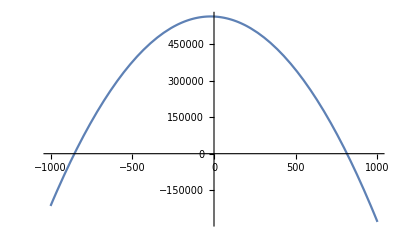

```mathematica
Plot[(minET)/.{cosy->0.9,cosphi->0,Epp->1000,mi->0,mir->200,Eq->150,pxq->10},{pzpp,-1000,1000},PlotRange->All]
```

```mathematica
Solve[pzpp==Epp-(mi^2-t)/(2Eap),t]//FullSimplify
```

{{t→mi^2+2 Eap (-Epp+pzpp)}}